# Programming in Mathematica - A Crash Course

Tao Ju, Washington University in St. Louis
Fall 2010

Mathematica is a powerful environment for scientific computing as well as rapid prototyping. The goal of this tutorial is to get someone who already has programming experiences in other languages up to speed with computing, coding, and visualization in Mathematica. To fully utilize this tutorial, evaluate the expressions contained in the notebook and try out the various exercises (marked in this style).

Acknowledgement: the tutorial is in part based on the COMP110 modules at Rice University (authored by Joe Warren).

## Survival skills for Mathematica

Mathematica consists of two main parts;  a front-end and a kernel.  The front-end is a set of windows that allows the user to view Mathematica files, called notebooks, and manipulate the contents of these notebooks.  The kernel is a set of core mathematical functions that Mathematica uses to compute the value of expressions that appear in Mathematica notebooks. Across the top of the screen is a thin, but wide window that contains a number of pull-down menus.  These windows can be used to

Open and save notebooks (File).

Edit the contents of a notebook (Edit).

Format the contents of a notebook (Format).

Organize and manipulates cells, the building blocks of a notebook (Cell).

Create graphics for the notebook (Graphics).

Control evaluation of expressions in the notebook (Evaluation).

Open palette design to simplify common tasks (Palettes).

Manage the layout of multiple notebooks on the screen (Window),

Provide helpful information about Mathematica (Help).

Instead of exploring each of these menus in detail, we will focus on a few key survival skills for Mathematica which can be accessed through these menus.

### Writing notebooks

Mathematica is not only a powerful computing tool, but also serves as a full-fledged document preparation environment. The document you are looking at right now is called a notebook, which can incorporate a variety of contents like texts, equations, figures and interactive graphics.

A Mathematica notebook consists of a sequence of cells.  Each cell has a particular style associated with it.  To view this style, you first select the cell by clicking on the square bracket bounding the cell on the right side of the window.  Next, select the Format menu and the Style submenu. (Alternatively, you can click on the square bracket with the right mouse botton, and access the Style menu.) The resulting drop-down menu lists the possible cell styles for the current notebook and has a check mark next to the style associated with the selected cell.  You may change the style of an existing cell using this menu.

Some cells such as the "Survival Skills in Mathematica" cell above act as titles or section heading that cause cells to be grouped together hierarchically.  If we select this cell and check its style, we note its style is Section.  All text cells in between two section cells make up the body of this section.  You can expand and collapse this section of the notebook by double clicking on the right bracket associated with the section heading (a cell with collapsed contents inside will have a small triangle at the bottom of the bracket). Mathematica uses a default hierarchy to group cells. For example, the Title cell is at the top level of the hierarchy, followed by Section, then SubSection, then SubSubSection. Adding cells for titles and sections makes your notebook look more polished.

Exercise: Fully expand the remaining sections in this notebook.

In most notebooks there are two important types of cells, Input cells and Text cells.  To create a cell, click on the space between any two existing cells and start typing. You may change the cell style as discussed above.The default cell type is Input cells, which contain Mathematica expressions waiting to be evaluated (and are shown in boxes).  Hitting Shift+Enter in an Input cell causes Mathematica to evaluate the contents of the cell and produce a corresponding Output cell.  On the other hand,  Text cells do not contain expressions that are destined to be evaluated.  Instead, they contain text and formulas that are meant to be read (like this cell).

Exercise: Create a new Text cell with and a new Input cell, and type "Hello World" in both cells. Try evaluating the Input cell, and what happens? Now, replace the words in the Input cell with a numerical expression (e.g., 2*3), and evaluate it.

“Hello World”

```mathematica
"Hello World"
6+2
```

Hello World

8

```mathematica
"Hello World"
```

A common beginner mistake is to punch all of their text into a single Text cell and try to format the text inside the cell.  A better method is to treat each Text cell as a single paragraph and let Mathematica handle the typesetting using the options in the Format menu. For more information on cells and notebooks, you should take a brief look at the tutorial Notebooks as Documents.

### Saving your work

Perhaps the most critical task is saving your work (use Save or Save As in the File menu). As a general piece of good advice, I suggest that you save your work frequently.  Computers (especially running Windows) have a bad habit of misbehaving at the most critical time (say after you have done an hour of unsaved work).  I suggest saving your work at least every 15 minutes or before evaluating a piece of code that could have unexpected outcomes.

### Getting help

The Documentation Center that is accessible from the Help menu will become your best friend in using Mathematica.  The main menu for the Documentation Center provides an overview of the capabilities of Mathematica.  Other ways to access information about a function are either to simply select the function name in your notebook and press F1 , or to type its name into the blank line at the top of the Documentation Center window and click the Mathematica icon to the left.  The Documentation Center will search for and return links to relevant topics in its library of helpful information.

Exercise: Use the Documentation Center to locate functions that manipulate prime numbers.  Locate a function that determines whether an integer is prime.  Use this function to determine whether 2^31-1 is prime.

```mathematica
PrimeQ[2^31-1]
```

True

The Documentation Center contains a number of tutorials on relevant topics in Mathematica.  Instead of rehashing them in our notebooks, I will simply provide a hyperlink to the relevant tutorial or explanation (shown in orange in this notebook).

Exercise: Click on the orange text to visit a tutorial on Integer and Number-Theoretical Functions.

### Controlling computation in Mathematica

One final skill is learning how to control computations in Mathematica.  Mathematica has no notion of an undefined variable.  While the idea that computation corresponds to simplification of an expression makes Mathematica an extremely powerful language, this paradigm sometimes causes Mathematica to strain mightily to simplify or evaluate an expression in which the user has unwittingly made a simple mistake such as accidentally inserting an undefined variable.

In such cases, Mathematica may take a long time to find what it thinks is the correct answer to an erroneous input expression.  If Mathematica "hangs" and fails to return a reasonable answer in a moderate amount of time, this situation is often the case.  To help deal with this problem, you may abort a current evaluation by selecting the Abort Evaluation option from the Evaluation menu.  (This command also has the keyboard shortcut Alt+. .)

Exercise: Evaluate the expression below. Abort its evaluation once you realize it will never return an answer.

```mathematica
While[True,1]
```

$Aborted

Occasionally, Mathematica may also run slowly due to the presence of lots of complex Manipulate commands.  Mathematica uses much of its computation power dynamically updating the output of these Manipulate commands (even if the user is not manipulating the sliders.)  If Mathematica seems to be laggy, you should try disabling Dynamic Updating in the Evaluation menu.

Exercise: Evaluate this expression with dynamic updating turned on.  Move the slider.  Next, disable dynamic updating.  Now, what happens when you move the slider?  Finally, enable dynamic updating once more and move the slider.  What happens?

```mathematica
Manipulate[x!,{x,0,100,1}]
```

## Mathematical expressions

Mathematica at its core is just a very sophisticated calculator.  To use this calculator, you need to create (or reuse) an Input cell and enter an expression.  Hitting Shift+Enter then evaluates the expression in the cell and returns its value (a simplified version of the expression). There are two basic forms of mathematical expressions, numerical and algebraic.

### Numerical calculations

Mathematica gives the user the ability to typeset mathematical expression in a quick and easy to use way.  For example,

```mathematica
1+2×3
5.0/7.5
√(2.2-0.9)
```

7

0.666667

1.14018

For novice users, the easiest way to create these math expressions is to use the BasicMathInput palette from the Palette menu.  This palette contains most of the interesting expressions that you might like to create. As you become more proficient at using Mathematica, you will start to become interested in using keyboard shortcuts to create most of these expressions.  Many of these shortcuts involve using either the control key or the escape key.  Take a brief look at the tutorial Entering Two-Dimensional Input for more a detailed description of how these shortcuts work.

The above form of mathematical expressions is called the TraditionalForm.  Internally, Mathematica represents all expressions in StandardForm.  This form consists of expressions of the form Function[arg_1,arg_2,…,arg_n].   For example, the expressions above in StandardForm is

```mathematica
Plus[1,Times[2,3]]
Divide[5.0,7.5]
Sqrt[Subtract[2.2,0.9]]
```

7

0.666667

1.14018

There are two key points to make about StandardForm. First, all Mathematica function names start with upper case.  (To distinguish your functions from Mathematica's, you should always use lower case.)  Second, the parameters to the function (the arg_i) are contained inside square brackets, not parentheses.  Specifically, Mathematica uses [] for functions and () for grouping inside expressions.  Square brackets and parentheses are not interchangeable.  For example,

```mathematica
Plus(1,1)
```

yields an error.  This error is indicated by the red bracket on the right-hand side of the cell with a small square labeled with a +.  To view the error message associated with Mathematica's evaluation, you can click on the + to expand the cell.  Confusing the usage of square brackets and parentheses is the most common error that a novice Mathematica user makes.  Please remember the difference.

In general, Mathematica has almost every mathematical function that you can imagine already available.  Remember to check Documentation Center when you are in need.

### Algebraic calculations

One fundamental feature of Mathematica that separates it from other languages like Java or Matlab is its ability to perform not only numerical calculations, but also algebraic calculations.  This ability arises because Mathematica treats a mathematical expression as something to be simplified as opposed to something to be evaluated numerically.  Thus, Mathematica is easily able to evaluate

```mathematica
(x+x)/x
```

2

without having a specific value for x, or

```mathematica
Expand[(x+y)^3]
```

x^3+3 x^2 y+3 x y^2+y^3

without having a specific value for x or y. You can learn more about symbolic and algebraic computations in the tutorials on Algebraic Calculations.

Given its ability to manipulate algebraic expressions, Mathematica is also well-suited to solving systems of algebraic equations. The bread-and-butter function for this task is Solve.

```mathematica
Solve[2x+1==0,x]
```

{{x→-1/2}}

Before pointing you towards the tutorial on Solving Equations for more reading, let me make two points about equations in Mathematica.  First, Mathematica uses double equals (==) for equations and single equals = for assignment.  Confusing the two is another common mistake in Mathematica.  Note what happens if we replace == by = in the expression above.

```mathematica
Solve[2x+1=0,x]
```

Set::write: Tag Plus in 1 + 2\ x is Protected.

Solve::eqf: 0 is not a well-formed equation.

Solve[0]

Solve (and many more Mathematica) functions can take not only a single equation as input, but also a list of equations.  Lists in Mathematica consist of a sequence of expressions, separated by commas and enclosed by curly brackets.  For example,

```mathematica
Solve[{x+y==4,x-y==0},{x,y}]
```

{{x→2,y→2}}

We will learn much more about lists in later sections.  While Solve returns exact answers and even symbolic ones (e.g., when the coefficients of the equations contain undefined symbols), a faster and more robust routine for finding approximate numerical answers is NSolve. For linear system of equations, a specialized routine is called LinearSolve.

### Exercises

Exercise 1: Typeset these expressions by yourself. Try some other mathematical expressions with powers, integrals, derivatives, or matrices, and evaluate the results.

```mathematica
1+2×3
5.0/7.5
√(2.2-0.9)
1+2*3

5.0/7.5

Sqrt[2.2-0.9]

498^2

∫(x+x^4) ⅆx

f[x_]=x^4 (x-2)-x^2

f'[x]

a={{2,5,9},{8,10,9}}.{2,4,5}
```

7

0.666667

1.14018

7

0.666667

1.14018

248004

x^2/2+x^5/5

-x^2+(-2+x) x^4

-2 x+4 (-2+x) x^3+x^4

{69,101}

Exercise 2:  Compute the value of the sum of the integers from 1 to 30 inclusive.  Instead of typing in the thirty numbers, use the Documentation Center to locate a function in Mathematica that performs this computation.  Find at least two functions that can handle this task.

```mathematica
Sum[i, {i, 30}]

∑_(i=1)^30 i

Total[Range[30]]
```

465

465

465

Exercise 3:  Given two number a and b, the absolute error between the two numbers is |a-b| while the relative error between the two number is (|a-b|)/a.  To 20 significant digits, what are the absolute and relative errors between π and 22/7?

```mathematica
a=Pi

b=22/7

SetAccuracy[Abs[a-b],20]

SetAccuracy[Abs[a-b]/a,20]
```

π

22/7

0.001264489267349619

0.000402499434770682

Exercise: Use Mathematica to find the solutions to the quadratic equation a x^2+b x+c==0.  Backsubstitute the Mathematica's answer into the equation and show the answers are actual solutions to the equation (check out the ReplaceAll function for substitution, and the Simplify function for reducing an algebraic expression to its simplist form).

```mathematica
Clear[a,b]

eq=a*x^2+b*x+c==0

v=Solve[eq,x]

eq/.{a->1,b->2,c->1}

v/.{a->1,b->2,c->1}

Simplify[v/.{a->22,b->11}]
```

c+b x+a x^2==0

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

1+2 x+x^2==0

{{x→-1},{x→-1}}

{{x→1/44 (-11-√(121-88 c))},{x→1/44 (-11+√(121-88 c))}}

## Variables

In Mathematica,  a variable can assume any kind of value that a Mathematica expression would return: number (Integer, Real, Complex, etc.), boolean expression (True or False), string, graphics, dynamic objects, etc., and even a function. There are two kinds of variables, ones that are reserved by Mathematica with constant values (which typically start with an uppercase letter), and ones that the user define (which are suggested to start with a lowercase letter).

In the last part of this section, we will discuss the scope of variables, and introduce one of the most useful functions in Mathematica for programming - Module.

### System constants

Several variables and symbols are reserved by Mathematica to hold values of well-known constants, such as ⅇ, ⅈ, π and ∞ (positive infinity). Their corresponding letter variables are E, I,  Pi and Infinity. For example,

```mathematica
Pi
```

π

Mathematica treats these constants as symbolic forms during evaluation untill they are explicitly asked to evaluate to numerical numbers (e.g., by calling functions such as N). However, this also means that the computation can be rather slow. For faster numerical evaluations, a good practice is to first cast these symbols to numberical numbers by N before using them in computation:

```mathematica
N[Pi]
```

3.14159

### User-defined variables

User-defined variables, by convention, always start with a lowercase letter to distinguish them from Mathematica's built-in constants and functions. The variable name can be made up of letters, numerics, and symbols.  Unlike other languages such as C or Java, there is no need to declare the type of the variable, and a same variable can be assigned with values of different types.  Variables values are set via the assignment operator =. For example,

```mathematica
r =10
α = 4π
```

10

4 π

Mathematica uses different font colors to differentiate variables that have been assigned a value and those that have not. Note that the color of the two variables r and α changed after you evaluated the cell above. Variables can be assigned with expressions involving other variables, and only the values (not the reference) of these other variables are used in the assignment. For example, let's define a new variable computed from r and α:

```mathematica
area = α r^2
```

400 π

Changing the value of variable  r will not affect the value of area:

```mathematica
r=20
area
```

20

400 π

Note that Mathematica displays the values of every expression we typed. Sometimes this is undesirable, especially if there are multiple expressions to be evaluated in order and you only care about the final result. To supress the display of results of an expression, end the expressions with a semicolon (;):

```mathematica
r =10;
α = 4π;
area = α r^2
```

400 π

### Scoping and Module

The variables in the above examples all have a global scope. That is, changing the value of the variable anytime in the current Mathematica session (even in different notebooks) would affect all computations involving that variable. To clear the content of a variable, use the Clear command,  which will make the variable an undefined symbol. For example:

```mathematica
a=1
```

1

now note how the color of the variable a changes after its content is cleared:

```mathematica
Clear[a];
a
```

a

Oftentimes it is useful to create local variables that are only shared among a block of code, for example, within a function. Such a block can be easily created with the function Module[{x,y,...},expr], which specifies that occurrences of the symbols x, y, …  in expr should be treated as local. Consider the following code:

```mathematica
a=10;b = 10;
Module[{a},
a =20;b=20;
a+b]
a+b
```

40

30

The reference to a in the body of Module does not affect the global variable, since a local variable with the same name is declared in Module. On the other hand, the referece to b in the body of Module affects the global variable. Local variables are colored differently than global variables in Mathematica.

The initialization of local variables in Module can take place within the starting curly brackets, for example:

```mathematica
Module[{a=20,b},b=10;a+b]
```

30

### Exercises

Exercise: Define two global variables a, b, and write a Module that swaps their values without creating any new global variables.

```mathematica
a=90;b=9999;

Module[{temp},temp=a;a=b;b=temp;]

Print["a = ",a," and b = ",b]
```

a = 9999 and b = 90

## Controlling program flow

Mathematica provides a comprehensive set of functions for controling program flow. We cover some basic ones here, and you should consult with tutorials in the Documentation Center for more information.  As we mentioned before, all Mathematica functions are called as foo[arg1,...] with arguments contained in square brackets.

### Print

Probably the most useful debugging function in Mathematica is the Print command, which we advise you to use often during coding. Print has a rather loose syntex, and can display any one or multiple expressions (e.g., numerics, string, graphics, dynamic objects, etc.). For example:

```mathematica
a=1;
Print["a's value is ",a];
```

a's value is 1

### Conditionals

Conditional functions utilize boolean expressions, which have values of either True or False. A boolean expression can be created by Relational Operators (e.g., <,>,==,≥,≤,≠ ), for example:

```mathematica
∞==∞
```

True

Some Mathematica built-in functions also return a boolean value. These functions are called Testing Expressions. The names of these functions all end with an uppercase Q. For example, the following function tests whether an integer if even:

```mathematica
EvenQ[1]
```

False

You can also combine boolean values using Logical Operators such as And (&&) and Or (||):

```mathematica
∞==∞&&EvenQ[1]
∞==∞||EvenQ[1]
```

False

True

The most common conditional function is If[condition,t,f], which evaluates the boolean expression condition and evaluate t if condition is True or f otherwise. A boolean expression can be either a comparison (using <,>,==,≥,≤,≠ ) or a function that returns For example:

```mathematica
If[∞==∞,1,2]
If[∞≠∞,1,2]
```

1

2

One of t,f can be omitted, and nothing will happen if they are chosen to be evaluated. For example:

```mathematica
If[∞==∞,1]
```

1

```mathematica
If[∞≠∞,1]
```

Calling If with a non-boolean expression would cause Mathematica to output the un-evaluated expression:

```mathematica
If[∞,1,2]
```

If[∞,1,2]

You can nest expressions to create more complex expressions:

```mathematica
If[∞==∞,If[∞==π,1,2],3]
```

2

Other conditional functions include Which, which tests a set of boolean expressions in turn, and Switch, which is similar to the switch/case command in C and Java. See tutorials on Conditionals for more functions and examples.

### Loops

The For[start,test,incr,body] command has a similar syntex to C and Java, executing start, then repeatedly evaluates body and incr until test fails to give True. For example:

```mathematica
For[i=1,i≤3,i++,Print[i]]
```

1

2

3

The Do[expr,{i,i_min,i_max,di}] command is a more succinct way to write an iterative expression that uses an iterator i within a range of values [i_min,i_max] at a fixed increment di. The following expression achieves the same effect as the one above:

```mathematica
Do[Print[i],{i,1,3,1}]
```

1

2

3

Note that the iterator i in Do is a local variable whose scope is only within the body of Do . The i_min part can be omitted if it is 1, and so is the increment di if it is 1:

```mathematica
Do[Print[i],{i,3}]
```

1

2

3

Using Do , You can create nested loops by using multiple iterators:

```mathematica
Do[Print[i,",",j],{i,3},{j,2}]
```

1,1

1,2

2,1

2,2

3,1

3,2

the above expression achieves the same effect as the following expression using For:

```mathematica
For[i=1,i≤3,i++,For[j=1,j≤2,j++,Print[i,",",j]]]
```

1,1

1,2

2,1

2,2

3,1

3,2

Another function of interest is While[test,body], which evaluates test, then body, repetitively, until test first fails to give True. For example:

```mathematica
a=1;
While[a≤3,Print[a];a++]
```

1

2

3

Mathematica provides functions Continue[] and Break[] that let you jump to next iteration of the loop or outside the current loop. For example, the following expression is equivalent to the one above:

```mathematica
a=1;
While[True,Print[a];a++;If[a>3,Break[]]]
```

1

2

3

See the tutorials on Loops and Control Structures for more usages of these functions and other related functions for looping control.

### Exercises

Exercise 1: Write an If expression that computes the absolute value of a variable y. Compare with the built-in function Abs.

```mathematica
y=-5

If[y≥0,y,-y]

Abs[y]
```

-5

5

5

Exercise 2: Using looping, print out the first 20 Fibonacci numbers. Compare with the built-in function Fibonacci.

```mathematica
fibonacci[n_]:=Module[{x=1,y=0,i=0},While[i++<n,{x,y}={y,x+y}];y]
For[i=1,i<=20,i++,Print[fibonacci[i]]]
Table[fibonacci[n],{n,20}]
```

1

1

2

3

5

8

13

21

34

55

89

144

233

377

610

987

1597

2584

4181

6765

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
Table[Fibonacci[n],{n,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

## Making new functions

Creating functions is a key component in programming in Mathematica. With functions, a large program can be built from smaller pieces that can be individually written, tested, and re-used. Mathematica treats functions as a type of variable, hence offering a lot of flexibility in working with functions (e.g., a function can be passed as argument to other functions).

By convention, user-defined functions in Mathematica always have names that begin with lower case letters (to differentiate from built-in functions).  There are different ways to create functions in Mathematica. While your will probably end up using the first approach for creating most of the standalone functions, the second approach can come handy for defining inline functions. We will also discuss a special type of function called memo functions, which have application in hashing.

### The first approach

Here is a simple user-defined function called myAbs that takes a single argument y and computes the absolute value of y:

```mathematica
myAbs[y_]:=If[y<0,-y,y]
```

The underscore _ after the variable y tells Mathematica that y_ is a pattern (i.e. y is an parameter for the function).  In Mathematica, patterns are used to give names to parts of an expression that have a particular structure.  Anytime that Mathematica subsequently encounters an expression of the form myAbs[…], Mathematica will evaluate the … expression and assign its value to the variable y, whose scope is local within the function body (hence the difference in the color of y).  Then, myAbs will evaluate the right-hand side of its definition (If[y < 0, -y, y]) using this local variable y and return this value as its answer.

We can now evaluate myAbs using various expressions as argument,

```mathematica
myAbs[1+1]
myAbs[0*1]
myAbs[-1-1]
```

2

0

2

To reduce the number of errors that you will make in defining new functions using this approach, here are the Three Laws of Function Definition for Mathematica (in homage to Asimov's Three Laws of Robotics).

1. Always use square brackets in the function definition and function evaluation.

For example, use f[x_]:=x+3 instead of using f(x_)=x+3.

2. Always use := instead of = in your function definition.

For example, use f[x_]:=x+3 instead of using f[x_]=x+3.  Using SetDelayed (:=) causes your function not to be evaluated until you call it (and that's why there is no display of results after you evaluate the definition).  This behavior mimics how most other programming languages work. (Later you will make use of = once you have a rock solid understanding of the difference between how := and = behave).

3. Always remember to use an underscore after the arguments to your function.

For example, use f[x_]:=x+3 instead of using f[x]=x+3.

A more complex function with local variables other than the input arguments can be defined using the scoping command Module, as we have learned above. For example, here is a function fact that computes the factorial of an input, positive integer, which makes use of a local variable:

```mathematica
fact[n_]:=Module[{result=1},
Do[result*=i,{i,n}];
result]
```

```mathematica
fact[5]
```

120

Finally, it is also possible to define functions of several arguments or no argument.  For example, here is another fact function that computes the product of all integers between the two input numbers:

```mathematica
fact[m_,n_]:=Module[{result=m},
Do[result*=i,{i,m+1,n}];
result]
```

```mathematica
fact[3,5]
```

60

The following function clearFact has no argument, and clears the definition of fact (note how the color of the function name fact changes in the cell above when you evaluate clearFact):

```mathematica
clearFact[]:=Clear[fact]
```

```mathematica
clearFact[]
```

### The second approach

Alternatively, a function can be defined using the Function command, which provides a slightly different format than the approach above. For example, here is a myAbs function equivalent to the one defined above:

```mathematica
myAbs=Function[{y},If[y<0,-y,y]];
```

The first part of Function declares a single argument of this function to be used as a local variable in the body, and the second part is the body. Now we can evaluate it just as before:

```mathematica
myAbs[1+1]
```

2

You can define a function with zero or multiple arguments too. Here is a function that returns true if both arguments are positive:

```mathematica
bothPos=Function[{x,y},And[x>0,y>0]];
```

```mathematica
bothPos[2,-1]
bothPos[2,1]
```

False

True

Function is often used to write inline functions that do not need a function name. There are variations of the syntax of Function that can make the code look more succinct. For example, I can equivalently define the above two functions, myAbs and bothPos as:

```mathematica
myAbs=If[#<0,-#,#]&;
```

```mathematica
bothPos=And[#1>0,#2>0]&;
```

Here the & symbol indicates this is a Function expression. The arguments to the function are referred to in the body by #, if it's a single-argument function, or by #1,#2,..., if it's a multiple-argument function. Below is an example where myAbs is defined as an inline function to get the absolute value of every element in a list (the Mathematica Map[f,expr] function applies a function f to every element of a list expr):

```mathematica
Map[If[#<0,-#,#]&,{1,-3,ⅇ,-π}]
```

{1,3,ⅇ,π}

### Memo functions and hashing

As mentioned above in the first approach, the SetDelayed (:=) is used to cause your function not to be evaluated until you call it - which is exactly how a regular function should behave. At times, however, you may want the function to "remember" the result of an evaluation, to avoid repeating the evaluation if the same argument is passed to the function. This is when Set (=) becomes useful.

Consider the following recursive function for computing the first n Fibonacci numbers:

```mathematica
fib[n_]:=If[n==0,0,If[n==1,1,fib[n-2]+fib[n-1]]];
```

Evaluate the function for some large n:

```mathematica
fib[40]
```

$Aborted

You may notice that the evaluation takes a long time. Hit  Alt+. to abort Mathematica's evaluation process.

To see why the evaluation is slow, observe that the function makes numerous calls to itself with the same arguments (the number of calls made to fib[n-k] during evaluation of f[n] is exactly the k+1th Fibonacci number.). Since the function has no "memory", each call needs to be evaluated, hence incurring a huge waste in time. Now, revise the function to include a Set (=) operation:

```mathematica
fib[n_]:=(fib[n]=If[n==0,0,If[n==1,1,fib[n-2]+fib[n-1]]]);
```

The trick here is that we assign the construct fib[n] with the resulting value of evaluation when fib is called the first time with argument n. From then on, any later calls to fib[n] will simply look-up the value associated with the construct fib[n] without evaluating the function body of fib. Now we can evaluate the function with much larger n and not getting laggy:

```mathematica
fib[100]
```

354224848179261915075

You can find more discussion on this trick in the tutorial on Memo Functions.

Another scenario when memo functions become useful is defining a hash map. A hash map is a way of storing values that can be quickly accessed with some keys. We can make use of the "look-up" capability of memo functions to build a simple hash map. For example, to define a hash map with one key and a default value of 0, we start off with a regular function:

```mathematica
hash[key_]:=0;
```

With this function alone, evaluating hash with any input key will return 0 (the default value). To store a value 1 associated with a key called "Monday", use the Set (=) operator:

```mathematica
hash["Monday"]=1;
```

Future evaluations with this key will cause Mathematica to look up the value 1, while evaluations with other keys will fall back to evaluating the original function hash, which would return 0:

```mathematica
hash["Monday"]
```

1

```mathematica
hash["Tuesday"]
```

0

### Suggestions for coding style

By now you have learned the essential tools to start programming in Mathematica. A common pitfall of novice programmers in Mathematica is to create a single, long function that does a complicated task. My first suggestion is divide-and-conquer: break big functions into smaller helper functions, each performing an atomic task. This will not only make your program more readable, but more importantly, makes debugging and testing a lot easier. Mathematica does not have a sophisticated debugging interface as in other languages suchas C++. Hence the smaller the function, the easier it is for you to figure out where it went wrong.

My second suggestion to improve readibility of the code is to add comments. Comments can be added either as a Text cell, or within an input expression between (* *). Here is an inline comment example:

```mathematica
fib[n_]:=If[n==0,
(* base case 1, return 0 *)
0,
If[n==1,
(* base case 2, return 0 *)
1,
(* otherwise, evaluate recursively *)
fib[n-2]+fib[n-1]]]
```

### Exercises

Exercise 1: Write a function fact[x] that computes the factorial of x using recursion. That is, your function body will contain calls to the same function. Try your function on various integers and compare with Mathematica's built-in Factorial function.

```mathematica
fact[n_]:= If[ n==0,1,n*fact[n-1]]
fact[10]
Factorial[10]
```

3628800

3628800

Exercise 2: Re-define your recursive function  fact[x] in the previous exercise using Function.

```mathematica
fact=Function[{y},If[y==0,1,y*fact[y-1]]];
fact[20]
```

2432902008176640000

Exercise 3: Create a hash map with two keys, and try storing and querying some values.

```mathematica
hash[key1_,key2_]:=0
hash["Monday","Tuesday"]=1
hash["Monday","Tuesday"]
hash["Sunday","T"]
```

1

1

0

## Lists

The most important and unique data type in Mathematica is the list.  There are well over a thousand Mathematica built-in functions that operate directly on lists, making lists a central construct in Mathematica. A list consists of a sequence of items enclosed by curly brackets and separated by commas.  For example, the list consisting of the numbers 1, 2, 3, and 4 has the form:

```mathematica
{1,2,3,4}
```

{1,2,3,4}

Note that internally, Mathematica represents this list in the form List[1,2,3,4].

Lists can be nested. For example, here is a two-dimensional array of numbers:

```mathematica
{{2,3},{3,4},{4,5}}
```

{{2,3},{3,4},{4,5}}

More generally, lists can be a sequence of any Mathematica expressions:

```mathematica
{True,{2+a,π,{Sin[x]}},"Hello"}
```

{True,{12,π,{Sin[x]}},Hello}

In the following we will cover some most commonly used list operations. This section just skims the surface of Mathematica's capabilities concerning lists. If you have time, read through the section List Manipulation to get a better idea of Mathematica's list capabilities.

The exercises are listed at the end of the section. You will be using list operations for creating and processing 2D images.

### Creating lists

There are several ways to create lists in Mathematica.  The easiest way is simply to enumerate the entries in the list as done above - if they are few. For larger lists, a number of built-in functions can be used to simplify the creation process.

The function Range[i_min,i_max,di] offers a simple way to create a list of numbers with regular intervals (it has several simpler variants, e.g., when d_i=1 or i_min=1):

```mathematica
Range[0,5,0.5]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

More often, we wish to build a list by evaluating an expression at regular intervals. The most useful function for this purpose is Table. It has many variations of syntax (click on the hyperlink to see for yourself), and they are similar to the syntax of Do. In the simplest form, Table[expr,{i_max}] generates a list of i_max copies of expr. For example, the following produces a list of one hundred 1s:

```mathematica
Table[1,{100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

The full syntax is Table[expr,{i,i_min,i_max,di}], which generates a list of values of expr when i runs from i_min to i_max with intervals di. For example, the following generates a list of numbers that are square roots of the numbers we generated above with Range:

```mathematica
Table[Sqrt[x],{x,0,5,0.5}]
```

{0.,0.707107,1.,1.22474,1.41421,1.58114,1.73205,1.87083,2.,2.12132,2.23607}

Nested lists can be created easily with Table (just like Do). For example:

```mathematica
Table[{i,j},{i,3},{j,2}]
```

{{{1,1},{1,2}},{{2,1},{2,2}},{{3,1},{3,2}}}

### Querying lists

Here are some useful functions to get quick facts about a list, such as its size, data range, and the location of a particular element.

Length gives the number of elements on the first level of a list:

```mathematica
Length[{1,2,3,4}]
Length[{{2,3},{3,4},{4,5}}]
```

4

3

For a multi-dimensional array, Dimensions gives the length of the array in each dimension:

```mathematica
Dimensions[{1,2,3,4}]
Dimensions[{{2,3},{3,4},{4,5}}]
```

{4}

{3,2}

The MemberQ[l,e] function checks whether a list l contains a particular element e:

```mathematica
MemberQ[{1,2,3,4,3},3]
```

True

If you want to know the location(s) of the element in the list, use the Position[l, e] function:

```mathematica
Position[{1,2,3,4,3},3]
```

{{3},{5}}

The positions are returned as a list, and each element in the list is the index of one instance of e in l. Note that the index in a list in Mathematica starts from 1, not 0. If l is a nested list, each instance is represented by indices at succesively deeper levels:

```mathematica
Position[{{2,3},{3,4},{4,5}},3]
```

{{1,2},{2,1}}

Here, {1,2} represents the position at index 2 in the 1st sub-list, {2,1} represents the position at index 1 in the 2nd sub-list.

### Retrieving elements

The most common way to retrieve elements from a list is Part[l,i], which returns the ith element of the list l.  This function is used so often that Mathematica supports the shorthand form l[[i]] or l⟦i⟧.  (The special bracket ⟦ are formed by typing Escape [[ Escape.). For example:

```mathematica
l={1,2,3,4};
Part[l,3]
l[[3]]
l⟦3⟧
```

3

3

3

As mentioned before, Mathematica indices start from 1, not 0. Accessing a part of a list that does not exist is a common error in coding. Take the 0th element will yield nonsense (the value List), and taking elements after the end of the list will generate an error message. For example:

```mathematica
l⟦0⟧
l⟦5⟧
```

List

Part::partw: Part 5 of {1, 2, 3, 4} does not exist.

{1,2,3,4}⟦5⟧

An element in a nested list can be accessed by its indices at successively deeper level of the list, separated by commas:

```mathematica
a={{2,3},{3,4},{4,5}};
a⟦3⟧
a⟦3,2⟧
```

{4,5}

5

You can also retrieve multiple items from a list by using a list of indices instead of a single index. The result will be another list containing the subset of the original list with the specified indices. For example,

```mathematica
a⟦{1,3}⟧
a⟦{1,3},2⟧
```

{{2,3},{4,5}}

{3,5}

Part (⟦⟧) supports a powerful way of extracting a range of elements via the Span ;; operator. Spend a few minutes and read up on Span and Part.

Mathematica supports various other functions for element retrieval that serve specific needs. Functions First and Last return the first and last element of a list, respectively, and Rest and Most return the subset of the list without the first or last element, respectively. For example:

```mathematica
l={1,2,3,4,5};
First[l]
Last[l]
Rest[l]
Most[l]
```

1

5

{2,3,4,5}

{1,2,3,4}

Function Take[l,n] gives the first n elements of the list l,  Take[l,-n] gives the last n elements, and Take[l,{m,n}] gives elements m thgourh n:

```mathematica
Take[l,2]
Take[l,-2]
Take[l,{2,4}]
```

{1,2}

{4,5}

{2,3,4}

Similarly, function Drop[l,n] gives the list l without the first n elements,  Drop[l,-n] gives the list without the last n elements, and Drop[l,{m,n}] gives the list without elements m thgourh n. Also, Drop[list,{n}]gives the list without a single element at index n. For example:

```mathematica
Drop[l,2]
Drop[l,-2]
Drop[l,{2,4}]
Drop[l,{2}]
```

{3,4,5}

{1,2,3}

{1,5}

{1,3,4,5}

There are many other bulit-in functions that could simplify your code for retrieving elements, which are not covered here. Spend a couple of minutes and browse functions like Extract, Delete and Select.

### Modifying lists

Mathematica supports a range of functions for changing the structure of a list. A common task is to add a new element to an existing list. Mathematica offers functions Prepend, Append, and Insert for this purpose, which respectively adds an element to the beginning, the end, and at a specified locatoin of the list. For example,

```mathematica
l={1,2,3,4};
Prepend[l,0]
Append[l,0]
Insert[l,0,3]
```

{0,1,2,3,4}

{1,2,3,4,0}

{1,2,0,3,4}

Note that these functions (and most other Mathematica functions on lists) outputs the modified list but do not change the original list in the argument. For example, the variable l above is unaffected by these operations:

```mathematica
l
```

{1,2,3,4}

The two exceptions are functions PrependTo and AppendTo, which reset the content of the variable in the argument to be the result:

```mathematica
PrependTo[l,0]
l
```

{0,1,2,3,4}

{0,1,2,3,4}

There are a couple of functions used very often that change the ordering of elements in a list. Reverse reverses the order of elements, while RotateLeft or RotateRight cycles the elements to the left or right:

```mathematica
Reverse[l]
RotateLeft[l]
RotateRight[l]
```

{4,3,2,1,0}

{1,2,3,4,0}

{4,0,1,2,3}

Sort sorts the elements in ascending order:

```mathematica
Sort[{2,4,1,3}]
```

{1,2,3,4}

You can also defined a customized ordering function, using the inline function definition approach we discussed earlier (see section on Making new functions). For example, the following code sorts a nested list in descending order of the second element in each sub-list:

```mathematica
Sort[{{10,2},{30,1},{40,3}},#1[[2]]>#2[[2]]&]
```

{{40,3},{10,2},{30,1}}

Mathematica supports the usual operations involving multiple lists, such as Join, Union, Intersection, and Complement. While I will refer you to their reference pages for their syntax, I should point out that, except Join, the other three functions return a sorted list (in ascending order) without duplicate elements. Note the difference between Join and Union in this example:

```mathematica
Join[{3,1,2},{2,5}]
Union[{3,1,2},{2,5}]
```

{3,1,2,2,5}

{1,2,3,5}

### Vector and matrix operations

A number of Mathematica functions are designed for lists with a particular structure, such as 1D vectors and 2D matrices. These functions are essential for calculatoins in linear algebra. To start, the function MatrixForm is useful for viewing a 2D array in a matrix format:

```mathematica
a={{2,3},{3,4},{4,5}};
MatrixForm[a]
```

(2 | 3
3 | 4
4 | 5)

Transpose takes a 2D array and swaps its rows and columns:

```mathematica
Transpose[a]//MatrixForm
```

(2 | 3 | 4
3 | 4 | 5)

Common arithmatic functions (+,*,^,...) can apply directly to matrices (or vectors) of the same dimensions, in an element-wise manner. For example,

```mathematica
a+a//MatrixForm
```

(4 | 6
6 | 8
8 | 10)

Dot(.) performs matrix product, which requires the two input matrices to have compatible dimensions (the number of columns in the first matrix equals the number of rows in the second matrix):

```mathematica
a.Transpose[a]//MatrixForm
```

(13 | 18 | 23
18 | 25 | 32
23 | 32 | 41)

If the dimensions of the two matrices don't match, an error message will occur:

```mathematica
a.a
```

Dot::dotsh: Tensors {{2, 3}, {3, 4}, {4, 5}} and {{2, 3}, {3, 4}, {4, 5}} have incompatible shapes.

{{2,3},{3,4},{4,5}}.{{2,3},{3,4},{4,5}}

Note that if the two matrices are vectors, they can dot directly:

```mathematica
b={1,2,3};
b.b
```

14

Mathematica supports a comprehensive set of linear algebraic functions on matrices, such as Det, Inverse, Eigensystem, to name a few. Take a moment to browse this tutorial on Linear Algebra and see the capability of Mathematica in matrix operations.

### Applying functions to lists

Some Mathematica functions can be directly applied to a list to obtain a summary value, such Min and Max:

```mathematica
l={-1,2,-3,4};
Min[l]
Max[l]
```

-3

4

More often, a function needs to be applied to each element in the list, which requires iteration over the list. Although many Mathematica built-in functions automatically apply to every element in a list (check out for example Abs and EvenQ),  usually you need to use Table and Do to iterative over a list yourself. Both Table and Do need to use iterators over the indices in the list, which can make the code look complex. Mathematica supports two additional functions, Map and Scan, that can simplify your code.

The Map[f,l] function applies some function f to each element on the first level in l, and returns the result of evaluation in a new list with the same length as l. This is similar to Table, and in fact they are equivalent in uses. For example, both expressions below get the absolute value of each element in a list:

```mathematica
Map[If[#<0,-#,#]&,l]
Table[If[l⟦i⟧<0,-l⟦i⟧,l⟦i⟧],{i,Length[l]}]
```

{1,2,3,4}

{1,2,3,4}

The Map expression above uses an inline function, whose argument (an element in the list) is passed to the function body as #. Note that Map does not need to iterate over the indices, and hence the code is more succinct than Table. Check out some variants of Map, such as MapThread (iterating over multiple lists), and MapIndexed (passing the index of the element as well as the content to the function).

The Scan[f,l] function is similar to Map, except that it does not return any result. It achieves the same effect as Do, but simpler to write. For example, both expressions below print out values in a list:

```mathematica
Scan[Print["Element: ",#]&,l]
```

Element: -1

Element: 2

Element: -3

Element: 4

```mathematica
Do[Print["Element: ",l⟦i⟧],{i,Length[l]}]
```

Element: -1

Element: 2

Element: -3

Element: 4

### Exercises

List is the essential data structure for image analysis: a 2D image is simply a two-dimensional list, where each entry in the list is the color at a pixel. The following exercises use list operations to create images and implement several common image processing filters. Visualize your result with this helper function that displays a two-dimensional list as a 2D grayscale image (where the darker color indicates lower values):

```mathematica
showArray[arr_]:=Graphics[Raster[(arr-Min[arr])/(Max[arr]-Min[arr])], Frame -> True];
```

Exercise 1: Write a function makeImage[n,m] to create a 2D array with dimension n by m that evaluates Sin[x]*Sin[y] where x and y range between 0 and 2 π. Try your function with some values of n, m.

```mathematica
Clear[x,y]
makeImage[n_,m_]:=Table[Sin[x]*Sin[y],{x,0,2*Pi,2*Pi/(n-1)},{y,0,2*Pi,2*Pi/(m-1)}]
sth={{0.1,0.2,0.3},{0.2,0.43,0.4}}
showArray[sth];
Dimensions[sth];
makeImage[2,2];
makeImage[10,10];
showArray[makeImage[8,10]]
showArray[makeImage[40,40]]
```

{{0.1,0.2,0.3},{0.2,0.43,0.4}}

-Graphics-

-Graphics-

Exercise 2:  Thresholding: write a function threshold[img,val] that takes in an image img (represented as a 2D array) and some valuve val,  and returns a new image so that the value of a pixel is 1 in this new image if the corresponding pixel in img has value above val, and 0 otherwise. Apply your function to the result generated by your makeImage function.

```mathematica
threshold[img_, val_]:=Table[If[img[[i,j]]>val,1,0],{i,Dimensions[img][[1]]},{j,Dimensions[img][[2]]}]
pic2=threshold[makeImage[8,9],0.5]
showArray[threshold[makeImage[40,40],0.5]]
```

{{0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0},{0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0},{0,0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0}}

-Graphics-

Exercise 3:  Blurring: one way to add "blur" to an image is to replace the value at each pixel p (excluding those on the image boundary) with the average value of the 9 pixels in the 3 by 3 neighborhood of p.  Write a function blur[img] that takes in an image img and outputs the blurred image. Apply your function to the image generated by your threshold function, and examine what happens when you apply blurring repeatedly (check out the Nest function for repeated function evaluation).

```mathematica
blur[img_]:=Table[Which[i==1||i==Dimensions[img][[1]]||j==1||j==Dimensions[img][[2]],img[[i,j]],True,Mean[Mean[Take[img,{i-1,i+1},{j-1,j+1}]]]],{i,Dimensions[img][[1]]},{j,Dimensions[img][[2]]}]
pic4={{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}};
pic5={{0,0,0,0},{0,0.1,0.1,0},{0,0.01,0.02,0},{0,0,0,0}};
blur[pic4]
blur[makeImage[40,40]]
pic90=Nest[blur,pic2,3];
pic100=Nest[blur,pic2,4];
showArray[blur[pic4]];
showArray[pic2]
showArray[pic90]
showArray[pic100]
showArray[Nest[blur,pic2,6]]
showArray[Nest[blur,pic2,10]]
showArray[Nest[blur,pic2,100]]
showArray[Nest[blur,pic2,1000000]]
```

{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}}

$Aborted

```mathematica
showArray[Nest[blur,threshold[makeImage[40,40],0.5],10]]
```

-Graphics-

## Graphics

A picture is worth a thousand words. Mathematica has a powerful suite of graphics display functions, both in 2D and 3D. In general, these functions fall into two classes, ones for plotting graphs and ones for displaying general geometry (e.g., points, lines and polygons). We will discuss some commonly used functions in both classes.

### Plotting graphs

The function Plot[f,{x,x_min,x_max}] is a simple way to display the graph of a function f with a single variable x varying over the domain [x_min,x_max]. For example,

```mathematica
g[x_]:=1/(x^2+.001)
```

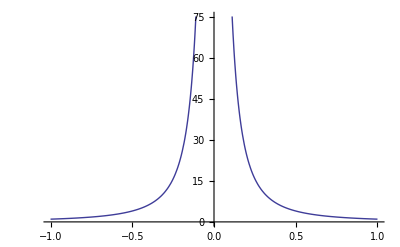

```mathematica
Plot[g[x],{x,-1,1}]
```

Note that in this particular plot, Mathematica has detected that the range of output values of g[x] is widely varying and automatically restricts the range (the y coordinates) to values from 0 to 70.  If you are unhappy with this choice, Mathematica provides a number of options that allow you to control the style of the output.  These options have the form Option→Value.  In our previous example, we can add PlotRange→All and force Mathematica to plot the entire range of values for g[x].

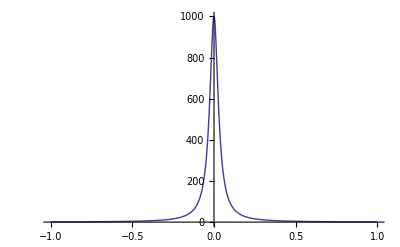

```mathematica
Plot[g[x],{x,-1,1},PlotRange->All]
```

Spend a couple of minutes browsing Mathematica's tutorial on Options & Styling to get a better feel for Mathematica's capabilities.

For functions of two variables, Mathematica provides three functions that provide reasonable visualizations.  As a test function, let's consider the function

```mathematica
g[x_,y_]:=Sin[x]Sin[y]
```

The simplest way to visualize h[x,y] is as a height surface drawn in 3D using the function Plot3D.

```mathematica
Plot3D[g[x,y],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

Note that this surface is a graphical object in 3D, and you can freely rotate (mouse dragging), translate (holding down Shift while dragging the mouse) and scale (holding down Crtl while dragging the mouse) the object in the viewing window.

An alternative way to visualize the behavior of this function is to draw the contours of the function using ContourPlot.  A contour is the set of all points {x,y} such that h[x,y]==c, where c is a constant. Contour lines are a standard method for visualization used in elevation charts.

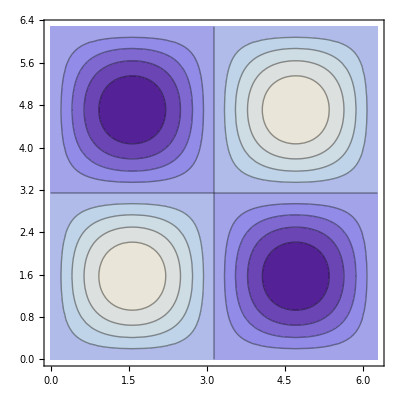

```mathematica
ContourPlot[g[x,y],{x,0,2π},{y,0,2π}]
```

Note that Mathematica automatically colors the areas between adjacent contours with a color that is approximately proportional to the value of the function in that area.  An alternative method is simply to create a 2D color image, where the color at a particular point is proportional to the value of the function.  Mathematica's DensityPlot provides this functionality.

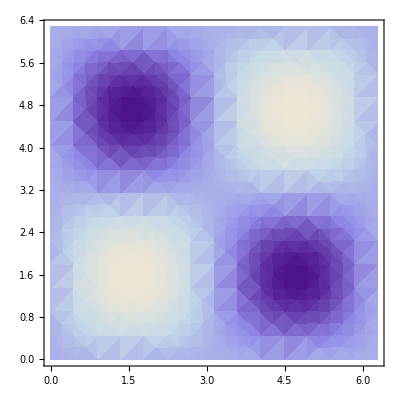

```mathematica
DensityPlot[g[x,y],{x,0,2π},{y,0,2π}]
```

Visualizing the behavior of functions in three variable is tougher.  The easiest method for visualizing these functions is to draw the 2D surfaces g[x,y,z]==c corresponding to various contours of the 3D function g[x,y,z].  In Mathematica, the function ContourPlot3D provides this functionality. Here is an example,

```mathematica
g[x_,y_,z_]:=x^2+2 y^2+4 z^2-1
```

```mathematica
ContourPlot3D[g[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

The above plotting functions evaluate an expression continuously over the specified domain. Mathematica also provides a set of discrete plotting functions that take in a array of values rather than a continuous function as their argument. The Mathematica tutorial Data Visualization summarizes these functions. A good rule of thumb is that if Mathematica has the function Foo that can visualize a continuous function, Mathematica also contains a function ListFoo that visualizes lists of data in a similar way. Let's get back to our function with one variable,

```mathematica
g[x_]:=1/(x^2+.001)
```

We can generate a list of values of g at regular intervals, and pass it to ListPlot to visualize:

```mathematica
glist=Table[g[x],{x,-1,1,.05}];
```

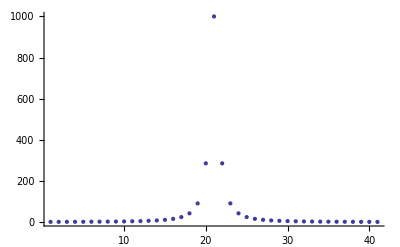

```mathematica
ListPlot[glist,PlotRange->All]
```

Note that ListPlot has plotted a set of points of the coordinates {i,glist⟦i⟧}. To make the plot have the correct range [-1,1]on the X axis, modifying the definition of glist to contain a list of points of the form {x,g[x]}.

```mathematica
glist=Table[{x,g[x]},{x,-1,1,.05}];
```

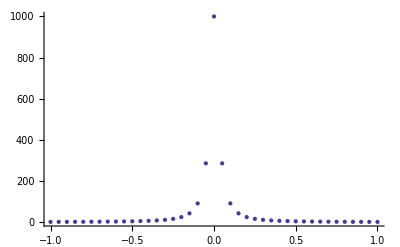

```mathematica
ListPlot[glist,PlotRange->All]
```

In many applications, we would like consecutive points joined by a line segment.  The option Joined→True does this.

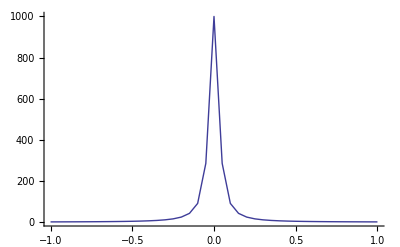

```mathematica
ListPlot[glist,Joined->True,PlotRange->All]
```

### Displaying geometry

The Graphics function provides essential drawing capabilities of 2D primitives, such as points, lines, polygons, etc, which have X,Y coordinates. For example, the following draws a filled square using the Polygon primitive:

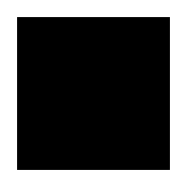

```mathematica
p=Polygon[{{0,0},{1,0},{1,1},{0,1}}];
Graphics[p]
```

Just like plotting, there are a range of rendering options you can use to adjust the look of the pictures. For example, the following draws the same square by with a pink fill color and a dashed, thick outline, using EdgeForm and FaceForm options (note that options should proceed the primitives in order to take effect):

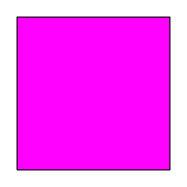

```mathematica
Graphics[{EdgeForm[{Dashed,Thick}],FaceForm[RGBColor[1,0,1]],p}]
```

Multiple primitives can be combined in one Graphics function, which will be drawn in the order they are given. The options for each primitive should be grouped with the primitive in a separate list. For example,

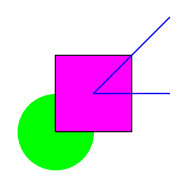

```mathematica
l=Line[{{1.5,1.5},{.5,.5},{1.5,.5}}];
Graphics[{
{Green,Disk[{0,0},.5]},
{EdgeForm[{Dashed,Thick}],FaceForm[RGBColor[1,0,1]],p},
{Blue,Thick,l}}]
```

A useful primitive for showing 2D images is Raster, which takes in a two-dimensional list of values (or RGB colors) and returns a rectangular array of gray (or RGB color) cells that can be displayed with Graphics. For example,

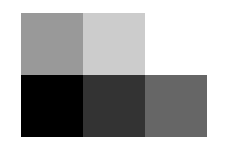

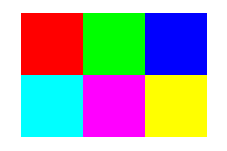

```mathematica
Graphics[Raster[{{0,0.2,0.4},{0.6,0.8,1}}]]
Graphics[Raster[{{{0,1,1},{1,0,1},{1,1,0}},{{1,0,0},{0,1,0},{0,0,1}}}]]
```

For drawing 3D primitives, Mathematica offers Graphics3D, which shares a similar syntax as Graphics but accepting geometry with 3D coordinates. The resulting 3D graphics allows rotating, shifting and scaling using mouse dragging. Here is a neat example from Mathematica (note that the option Opacity allows transparent rendering):

```mathematica
Graphics3D[{
{Blue,Cylinder[]},
{Red,Sphere[{0,0,2}]},
{Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}]},
{Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}]},
{Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}}]
```

-Graphics3D-

For a full description of available graphics primitives and drawing options in 2D and 3D, consult the respective guides on Graphics Objects, Graphics Directives , and 3D Graphics Options.

### Combining graphics

Different graphics objects (plots, or Graphics/Graphics3D primitives) can be combined in a same picture using the Show function. For example, you can generate a Plot graph with Point primitives on the graph:

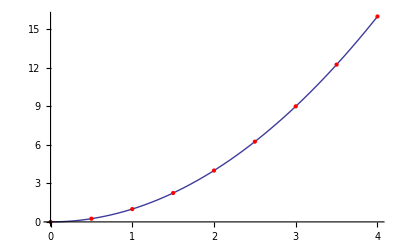

```mathematica
Show[Plot[x^2,{x,0,4}],Graphics[{Red,Table[Point[{x,x^2}],{x,0,4,.5}]}]]
```

You can also display multiple graphics objects in a grid format using GraphicsGrid, which takes a two-dimensional array of graphics objects. Here is an example where the grid is drawn explicitly due to the Frame → All option:

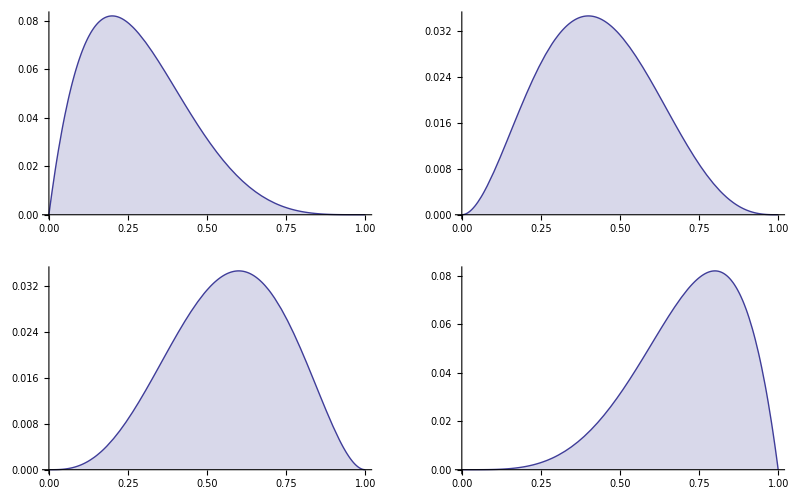

```mathematica
GraphicsGrid[{
{Plot[x(1-x)^4,{x,0,1},Filling->Axis],Plot[x^2(1-x)^3,{x,0,1},Filling->Axis]},
{Plot[x^3(1-x)^2,{x,0,1},Filling->Axis],Plot[x^4(1-x),{x,0,1},Filling->Axis]}},
Frame->All]
```

### Exercises

Exercise 1: Plot the functions Sin and Cos simultaneously over the domain {0,2π}.  Add a label to the X axis signifying that the input parameter is x and the two output functions are Sin[x] and Cos[x].  Fill the area under each curve.

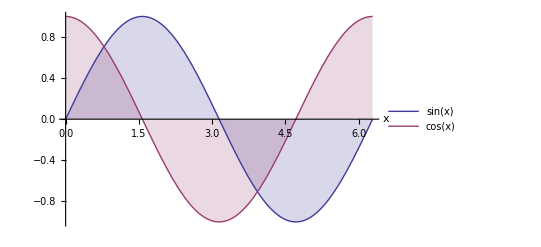

```mathematica
Show[Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotLegends->"Expressions",Filling->Axis,AxesLabel->{x,}]]
```

Exercise 2: Create a simple 3D scene with Graphics3D using 5 different kinds of primitives.

```mathematica
Graphics3D[{
{Yellow,Cylinder[{{0,0,-2},{0,0,2}},2]},
{Yellow,Sphere[{0,0,2},2]},
{Yellow,Sphere[{0,0,-2},2]},
{White,Cuboid[{-3,-3,-5},{3,2,-4}]},
{Pink,Cone[{{5,5,5},{3,3,3}},1]},
{Purple,Tube[{{-6,6,8},{-4,4,4}},1]}
}]
```

-Graphics3D-

## Dynamic visualizations

In the previous section, we have focused on creating static visualizations.  While these visualizations provide either 2D or 3D intuition, there remains one more dimension at our disposal to aid in understanding the behavior of a problem or its solution, time. Mathematica supports the creation of interactive visualizations in which users can manipulate a graphical object dynamically.  While Mathematica has lots of support for this activity, the key function for this task is Manipulate. In this section, I will cover the basics of Manipulate.  However, at some point, I suggest that you also review the tutorial Introduction to Manipulate.

### The Manipulate function

Manipulate is a function that takes two inputs:  an expression to be manipulated dynamically and a variable or a set of variables that can be changed dynamically to manipulate the expression.  Here is a simple example,

```mathematica
Manipulate[x!,{x,1,20,1}]
```

The power of Manipulate becomes more apparent when the expression is a Graphics object.  Here, the variables r, g, b create three sliders that control the color of a rectangle.

```mathematica
Manipulate[Graphics[{
RGBColor[{r,g,b}],
Rectangle[{-1,-1},{1,1}]}],
{r,0,1},
{g,0,1},
{b,0,1}]
```

Manipulate can also create a discrete set of buttons, when the variable can assume a finite set of choices.  Here, I allow x to be one of three discrete choices for an RGB color using three buttons.

```mathematica
Manipulate[Graphics[{
RGBColor[x],
Rectangle[{-1,-1},{1,1}]}],
{x,{{1,0,0},{0,1,0},{0,0,1}}}]
```

Below is a more interesting example in which I have attempted to make a blue disk of radius 0.1 revolve (following a unit circle) around a yellow disk of radius 0.2 fixed at the origin.

```mathematica
Manipulate[Graphics[{
RGBColor[{1,1,0}],
Disk[{0,0},0.2],
RGBColor[{0,0,1}],
Disk[{Sin[θ],Cos[θ]},0.1]}],
{θ,0,4π}]
```

Unfortunately, my Manipulate expression doesn't seem to work too well.  The problem is that Mathematica automatically trims the graphical output to tightly bound both disks.  Since the blue disk is moving, the bounding box is also moving ruining our sense of a blue disk orbiting a fixed yellow disk.  The solution to this problem is specify a fix PlotRange that always contains both disks.

```mathematica
Manipulate[Graphics[{
RGBColor[{1,1,0}],
Disk[{0,0},0.2],
RGBColor[{0,0,1}],
Disk[{Sin[θ],Cos[θ]},0.1]},
PlotRange->1.3],
{θ,0,4π}]
```

Mathematica can also manipulate the position of points that are not constrained to move along a 1-dimensional curve, but are free to move in two dimensions.  When you manipulate a scalar, Mathematica automatically creates a 1-dimensional slider;  when you manipulate a point, Mathematica automatically creates a 2-dimensional slider.  Below is an example of a 2-dimensional slider used to control the size of a blue rectangle by manipulating one of the corners of the rectangle.

```mathematica
Manipulate[Graphics[{RGBColor[{0,0,1}],Rectangle[{0,0},pt]},PlotRange->5,ImageSize->150,Axes->True],{pt,{1,1},{5,5}}]
```

You can replace 2-dimensional sliders with Locators -- points on the screen -- by specifying that you want a Locator attached to variable point.  You can then tug on the Locator instead of a slider to manipulate the point.

```mathematica
Manipulate[Graphics[{RGBColor[{0,0,1}],Rectangle[{0,0},pt]},PlotRange->5,ImageSize->150,Axes->True],{pt,{1,1},{5,5},Locator}]
```

### Exercises

Exercise 1: In the exercises of the Lists section, you created a threshold[img,val] function that binarizes an image img using a threshold value val. Now, create a function thresholdDyn[img] that produces a 1D slider that controls the threshold value to your threadhold function and dynamically displays the thresholded image.

```mathematica
thresholdDyn[img_]:=Manipulate[showArray[threshold[img,val]],{val,0,1}]
thresholdDyn[makeImage[20,30]]
```

Exercise 2: Replace the 1D slider in the previous problem with a 2D locator over the image img, and dynamically display the thresholded image with the threshold value set to be the pixel value at the locator.

```mathematica
Func1[img_]:=Manipulate[
showArray[threshold[img,img[[Round[pt[[2]]],Round[pt[[1]]]]]]],{pt,{1,1},{Dimensions[img][[2]],Dimensions[img][[1]]},Locator}]
Func1[makeImage[20,30]]
```

```mathematica
...
```